```mathematica
QS=Import["~/share/gpu-sampler/QS.csv"];
```

```mathematica
QS//Dimensions
```

{51200,8}

```mathematica
QS1=Transpose[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14}/.{x1->6-x11-x5,x2->6+x7+x8,x3->2-x14-x6-x8,x4->x10+x13-x5-x6+x7,x9->14-x10-x11-x13-x14,x12->-5+x13+x14}/.{x5->QS[[;;,1]],x6->QS[[;;,2]],x7->QS[[;;,3]],x8->QS[[;;,4]],x10->QS[[;;,5]],x11->QS[[;;,6]],x13->QS[[;;,7]],x14->QS[[;;,8]]}];
```

```mathematica
c={48, 28, 10, 7, 65, 7, 38, 15, 56, 48, 108, 24, 33, 19};
```

```mathematica
us1=Map[(c.#)&,QS1];
```

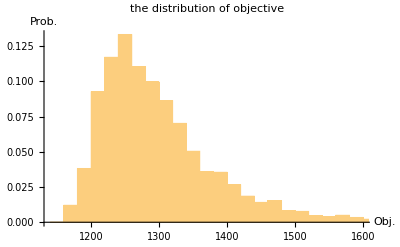

```mathematica
Histogram[us1,Automatic,"Probability",AxesLabel->{"Obj.","Prob."},PlotLabel->"the distribution of objective"]
```

```mathematica
ListPointPlot3D[QS[[;;,1;;3]],AxesLabel->{"x_1","x_2","x_3"},PlotStyle->Opacity[1],PlotLabel->"the scatter plot of the first three dimensions"]
```

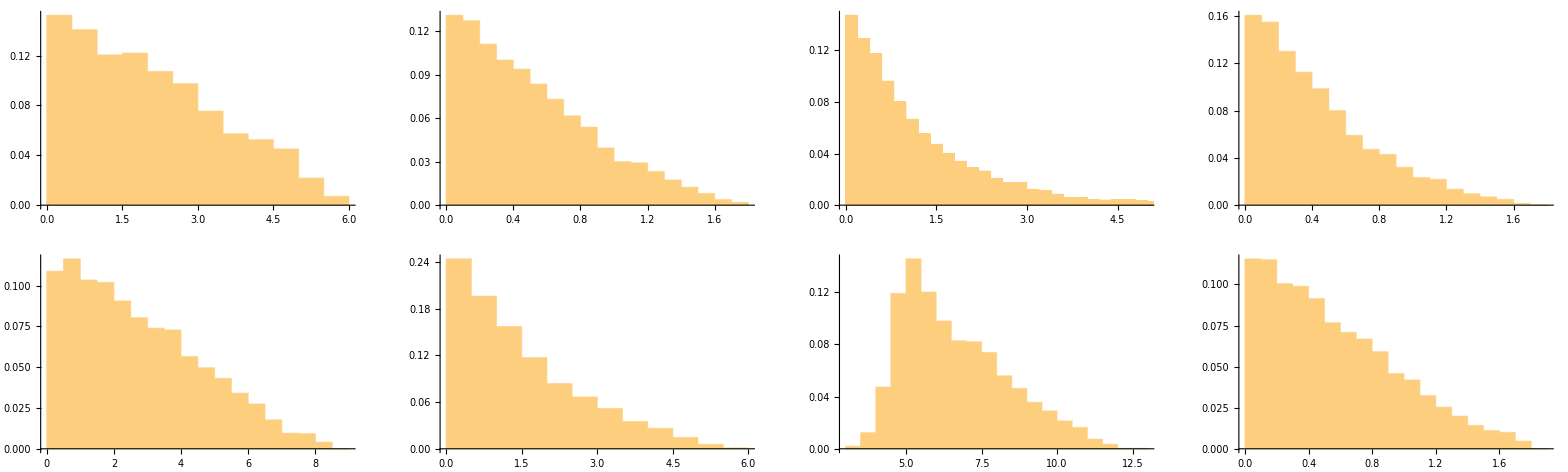

```mathematica
GraphicsGrid[ArrayReshape[Table[Histogram[QS[[;;,i]],Automatic,"Probability"],{i,1,8}],{2,4}]]
```

```mathematica
Min[us1]
```

1148.72